## Testing the signature formalism for the ^163Lu fit

## The fit uses the approach where TSD4 shares the same coupling scheme as the other three bands

the formulas for the first three bands are as follows:

TSD1 is the ground state with the coupling scheme j=13/2

TSD2 is the ground state at the same coupling scheme, but a different spin sequence. TSD2 is considered the signature partner band of TSD1

TSD3 is the 1-phonon excited state, built on top of TSD2, and it is in the same coupling scheme j=13/2

TSD4 is the 0-(or 1-)phonon excited band of this nucleus, built on top of TSD1 (with an excited phonon or just the ground state). It is the chiral partner band of TSD1, considered from the parity symmetry.

## Formulas

```mathematica
IF[I_]:=1/(2I);
B[I_,j_,A1_,A2_,A3_,V_,γ_]:=-(((2I-1)(A3-A1)+2j*A1)*((2I-1)(A2-A1)+2j*A1)+8A2*A3*I*j+((2j-1)(A3-A1)+2I*A1+V(2j-1)/(j(j+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]))*((2j-1)(A2-A1)+2I*A1+V(2j-1)/(j(j+1))2 √3 Sin[γ*π/180]));
C1[I_,j_,A1_,A2_,A3_,V_,γ_]:=(((2I-1)(A3-A1)+2j*A1)*((2j-1)(A3-A1)+2I*A1+V*(2j-1)/(j(j+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]))-4I*j*A3^2)*(((2I-1)(A2-A1)+2j*A1)*((2j-1)(A2-A1)+2I*A1+V*(2j-1)/(j(j+1))2 √3 Sin[γ*π/180])-4I*j*A2^2);
HMin[I_,j_,A1_,A2_,A3_,V_,γ_]:=(A2+A3)/2(I+j)+A1(I-j)^2-V*(2j-1)/(j+1)Sin[γ*π/180+π/6];
Omega1[I_,j_,A1_,A2_,A3_,V_,γ_]:=√(1/2(-B[I,j,A1,A2,A3,V,γ]-(B[I,j,A1,A2,A3,V,γ]^2-4C1[I,j,A1,A2,A3,V,γ])^(1/2)));
Omega2[I_,j_,A1_,A2_,A3_,V_,γ_]:=√(1/2(-B[I,j,A1,A2,A3,V,γ]+(B[I,j,A1,A2,A3,V,γ]^2-4C1[I,j,A1,A2,A3,V,γ])^(1/2)));
EWobb[n1_,n2_,I_,j_,A1_,A2_,A3_,V_,γ_]:=HMin[I,j,A1,A2,A3,V,γ]+Omega1[I,j,A1,A2,A3,V,γ](n1+1/2)+Omega2[I,j,A1,A2,A3,V,γ](n2+1/2);
TSD1[I_,A1_,A2_,A3_,V_,γ_]:=EWobb[0,0,I,6.5,A1,A2,A3,V,γ]-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
TSD2[I_,A1_,A2_,A3_,V_,γ_]:=EWobb[0,0,I,6.5,A1,A2,A3,V,γ]-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
TSD3[I_,A1_,A2_,A3_,V_,γ_]:=EWobb[1,0,I-1,6.5,A1,A2,A3,V,γ]-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
TSD400[I_,A1_,A2_,A3_,V_,γ_]:=EWobb[0,0,I,6.5,A1,A2,A3,V,γ]-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
TSD410[I_,A1_,A2_,A3_,V_,γ_]:=EWobb[1,0,I-1,6.5,A1,A2,A3,V,γ]-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
```

## Calculations

```mathematica
spin1={8.5,10.5,12.5,14.5,16.5,18.5,20.5,22.5,24.5,26.5,28.5,30.5,32.5,34.5,36.5,38.5,40.5,42.5,44.5,46.5,48.5};
spin2={13.5,15.5,17.5,19.5,21.5,23.5,25.5,27.5,29.5,31.5,33.5,35.5,37.5,39.5,41.5,43.5,45.5};
spin3={16.5,18.5,20.5,22.5,24.5,26.5,28.5,30.5,32.5,34.5,36.5,38.5,40.5,42.5};
spin4={23.5,25.5,27.5,29.5,31.5,33.5,35.5,37.5,39.5,41.5};
```

```mathematica
tsd1={0.1966,0.4597,0.7746,1.1609,1.6112,2.1265,2.7051,3.3441,4.0411,4.7937,5.5992,6.457,7.3667,8.3293,9.3458,10.4169,11.5431,12.7224,13.9491,15.2181,16.5221};
tsd2={1.3394,1.7467,2.2184,2.7527,3.3484,4.003,4.7143,5.4805,6.3004,7.1733,8.0998,9.08,10.1147,11.2036,12.3466,13.5441,14.7911};
tsd3={2.1237,2.6293,3.1973,3.8243,4.5094,5.2506,6.0465,6.8963,7.7988,8.7546,9.7638,10.8268,11.9392,13.0861};
tsd4={4.58,5.2251,5.9273,6.6819,7.4919,8.3573,9.2778,10.2535,11.2851,12.3701};
```

```mathematica
printer[spins_,tsd_,A1_,A2_,A3_,V_,γ_]:=Table[{spins[[i]],tsd[spins[[i]],A1,A2,A3,V,γ]},{i,1,Length[spins]}];
```

## The fit parameters

```mathematica
i1=76;i2=11;i3=6;v=0.1;γ=19;
```

```mathematica
shower[spins_,tsd_]:=Do[Print[printer[spins,tsd,IF[i1],IF[i2],IF[i3],v,γ][[i]]],{i,1,Length[spins]}];
```

## TSD1

```mathematica
shower[spin1,TSD1]
```

{8.5,0.272262}

{10.5,0.592782}

{12.5,0.962838}

{14.5,1.39803}

{16.5,1.88638}

{18.5,2.42732}

{20.5,3.02085}

{22.5,3.66697}

{24.5,4.36571}

{26.5,5.11705}

{28.5,5.92102}

{30.5,6.77759}

{32.5,7.68679}

{34.5,8.64861}

{36.5,9.66305}

{38.5,10.7301}

{40.5,11.8498}

{42.5,13.0221}

{44.5,14.2471}

{46.5,15.5246}

{48.5,16.8548}

## TSD2

```mathematica
shower[spin2,TSD2]
```

{13.5,1.17356}

{15.5,1.63563}

{17.5,2.15028}

{19.5,2.71751}

{21.5,3.33733}

{23.5,4.00977}

{25.5,4.73481}

{27.5,5.51246}

{29.5,6.34273}

{31.5,7.22561}

{33.5,8.16112}

{35.5,9.14925}

{37.5,10.19}

{39.5,11.2834}

{41.5,12.4294}

{43.5,13.628}

{45.5,14.8793}

## TSD3

```mathematica
shower[spin3,TSD3]
```

{16.5,1.65862}

{18.5,2.19092}

{20.5,2.77695}

{22.5,3.4165}

{24.5,4.10943}

{26.5,4.85559}

{28.5,5.6549}

{30.5,6.50728}

{32.5,7.41266}

{34.5,8.371}

{36.5,9.38226}

{38.5,10.4464}

{40.5,11.5634}

{42.5,12.7332}

## TSD4

```mathematica
shower[spin4,TSD400]
```

{23.5,4.00977}

{25.5,4.73481}

{27.5,5.51246}

{29.5,6.34273}

{31.5,7.22561}

{33.5,8.16112}

{35.5,9.14925}

{37.5,10.19}

{39.5,11.2834}

{41.5,12.4294}

## Plotting the energies based on the actual parameter values.

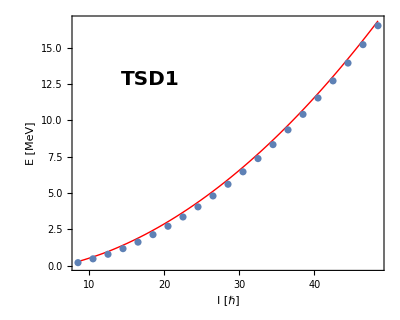

```mathematica
plot[spins_,band_,I1_,I2_,I3_,V_,γ_]:=Plot[band[x,IF[I1],IF[I2],IF[I3],V,γ],{x,spins[[1]],spins[[Length[spins]]]},AspectRatio->0.8,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Red},FrameLabel->{"I [ℏ]","E [MeV]"},Epilog->Inset[Style[StringTemplate["``"][band],Black,Bold,20,Italic,FontFamily->"Times New Roman"],Scaled[{0.25,0.75}]]];
showCombo[spins_,tsd_,band_,I1_,I2_,I3_,V_,γ_]:=Show[plot[spins,band,I1,I2,I3,V,γ],ListPlot[Table[{spins[[i]],tsd[[i]]},{i,1,Length[spins]}]]];
showCombo[spin1,tsd1,TSD1,i1,i2,i3,v,γ]
```